# Lab 6: Programming 1 -- Carter Colton

```mathematica
Clear["`*" ]
```

## Assignment 1: An Interesting RegionPlot

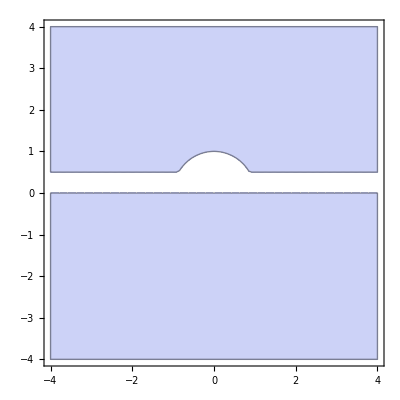
Create a RegionPlot that looks like this. The equation for the circular arc is x^2+y^2=1. The white horizontal stripe is where y is between 0 and 0.5. You will likely need both an && and an || in your RegionPlot.
-Graphics-

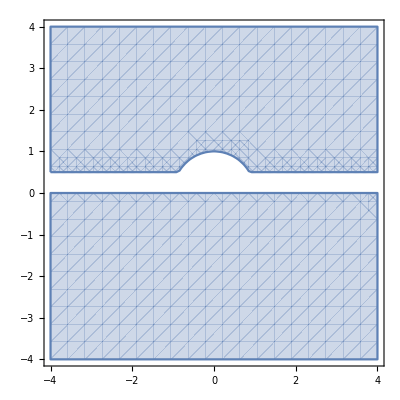

```mathematica
RegionPlot[(x)^2+(y)^2>1&&y>0.5||y<0 ,{x,-4,4},{y,-4,4}]
```

## Assignment 2: Using “Xor”

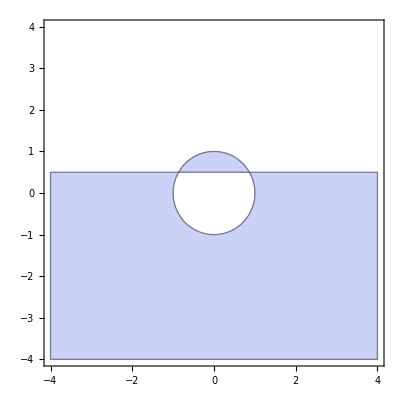
Use Xor to generate the following RegionPlot. (Note that unless you increase “PlotPoints” from the default, Mathematica will artificially chop off the sharp edges of the boundary.)

-Graphics-

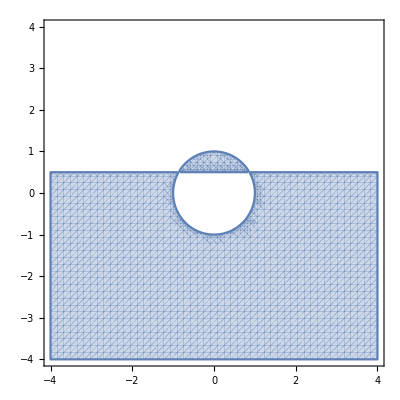

```mathematica
RegionPlot[Xor[x^2+(y)^2<1,-y>-.5],{x,-4,4},{y,-4,4},PlotPoints->50]
```

## Assignment 3: Using “If”

(a) Use If to create a function, myabs[x_], that mimics the Abs function.  Plot it over the range from {x, -3, 3}.
(b) Use If to create a function, happyprime[n_], that returns a  when n is a prime number and a  otherwise (you can copy/paste these icons into your function).  Then try it out on the integers from 1 to 10. Hint: read about the PrimeQ function.

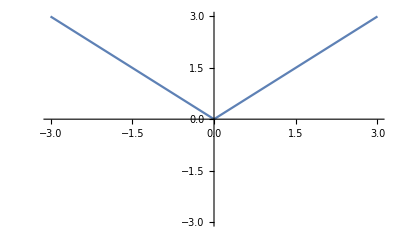

```mathematica
myabs[x_]:=If[x>0,x,-x]
Plot[myabs[x],{x,-3,3},PlotRange->{-3,3}]
```

```mathematica
happyprime[n_]:=If[PrimeQ[n],-Graphics- , -Graphics- ]
Table[happyprime[n],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Assignment 4: Using Which or Switch

Use Which or Switch to create a function that creates a plot of x if the input is equal to 1, a plot of x^2 if the input equals 2, a plot of x^3 if the input equals 3, and a plot of e^-x otherwise. That is, the output of the function should be the plots themselves. (That’s not a problem: functions can output numbers, or text strings, or plots, or any other kind of Mathematica objects you want.) All plots should go from x = -2 to 2. Take care that the function input is not called x, if you’re using x as the variable in the various Plot commands. Test it for inputs of 1, 2, 3, and 4.

```mathematica
Clear[t]
```





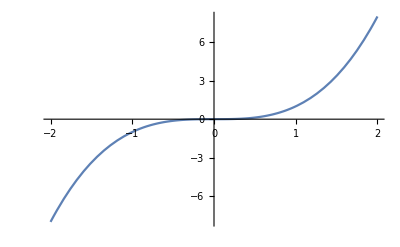

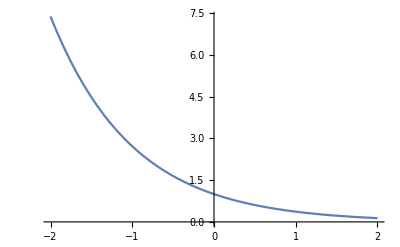

```mathematica
f[t_] := Plot[Switch[t, 1, x, 2,x^2,3, x^3,_,E^(-x)]  ,{x,-2,2}]
f[1]
f[2]
f[3]
f[4]
```

## Assignment 5: Using “Do”

(a) Use Do and  +=  to compute the sum of the integers from 1 to 100 and store the answer in a global variable named result. Display the answer after the loop is complete. Hint: initialize result to 0 (i.e. “result = 0;”) before starting the Do loop.
(b) Use Do to start with decimal number latest = 1.0, and recursively compute 100 cosines, taking the cosine of the most recent result each time.  Show the final value.
(c) In this example, I use a Do loop to accumulate a list of the integer sums of the form ∑ _(n =1)^p n  for p values running from 1 to 10.  Evaluate the example and figure out how it works.  Then modify it to accumulate a list of the squared-integer sums of the form  ∑ _(n =1)^p n^2. Tip: I recommend you copy this code to a different cell before you start modifying it.

```mathematica
result=0;
Do[result+=n,{n,1,100,1}]
result
```

5050

```mathematica
latest=1.0;
Do[latest=Cos[latest],{n,1,100,1}]
latest
```

0.739085

Regular Sum

```mathematica
resultlist = {}; result=0;
Do[ result+=p;resultlist = Append[resultlist,result], {p,1,10}]
resultlist
```

{1,3,6,10,15,21,28,36,45,55}

Squared integer sums

```mathematica
resultlist = {}; result=0;
Do[ result+=p^2;resultlist = Append[resultlist,result], {p,1,10}]
resultlist
```

{1,5,14,30,55,91,140,204,285,385}

## Assignment 6: Using “While”

Use While to create a list of the powers of 2 (i.e. 2^n) that are less than 10^6.  Hints: First define resultlist = { } and n=0  for future use.  Then, do a While loop. Inside the loop, test to see if 2^n<10^6 and if so use Append or AppendTo to add 2^n to resultlist; then increment n.

Side note: AppendTo is a shortcut for using Append to add to a list. The following two commands are exactly equivalent:
	resultlist = Append[resultlist,result]      (used above)
	AppendTo[resultlist,result]

```mathematica
resultlist={}; n=0;
While[2^n<10^6,AppendTo[resultlist,2^n];n++]
resultlist
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288}

## Assignment 7: Solving Cos[x]=x

Start with decimal number latest = 1.0, and use While to recursively compute cosines until the magnitude of the change between recursions is less than 10^-6.  In other words, keep evaluating  latest = Cos[latest] as long as Abs[Cos[latest]-latest]  > 10^-7.  Use a second global variable to count the number of iterations the loop goes through before the 10^-6 tolerance is reached. Display the answer along with the number of iterations.  In case it’s not obvious, when cos(x) - x = 0 to the desired tolerance, you’ve found the answer to the transcendental equation x = cos(x), doing the same sort of thing that the FindRoot command does internally. Congratulations! You can use FindRoot to check your answer if you’d like.

```mathematica
latest=1.0;n=0;
While[Abs[Cos[latest]-latest]  > 10^-7,latest=Cos[latest];n++]
latest
n
```

0.739085

39

## Assignment 8: Using “Nestlist”

Use NestList to create a function which accumulates a list of the next 5 prime numbers after a user-specified number (not including the number, even if it is prime). Hint: NextPrime should be quite helpful.

```mathematica
Clear[x]
```

```mathematica
list[x_]:=NestList[NextPrime[#]&,NextPrime[x],5];
```

Testing function at 4

```mathematica
list[4]
```

{5,7,11,13,17,19}

Testing function at 17

```mathematica
list[17]
```

{19,23,29,31,37,41}

## Assignment 9: Your First Two Modules

(a) It is traditional when learning a new programming language, that your first program should be to have the computer announce “Hello world”.  See this Wikipedia article for a bit more info, if you’d like. Let’s keep with tradition. Create a Module that takes one input, but outputs “Hello world” regardless of what the input is.

(b) Here’s a slightly harder task than “Hello world”. Use Module to create a pure function f1[xlist_] that takes a list of real numbers as input (unknown length), computes the Mean and the StandardDeviation of the list, subtracts the mean from each element of the list, divides each element of the resulting list by the standard deviation, then returns that list of numbers as the function’s output.  Try your new function out on a list of 100 RandomReal numbers that lie between 0 and 10.  The results should lie primarily between -1.5 and +1.5.  Plot a Histogram of the list to verify this.

Warning: This is important, so please read to spare yourself some grief. When you pass an argument into a Module from a function definition, such as the value of “x” when doing this function definition, f[x_] := Module[.....], you cannot change the value of x inside the Module. Trying to set x equal to something else will result in an error. If you want to modify the value, you have to set a local variable equal to x, and then modify the local variable instead.

```mathematica
g[x_]:=Module[{},
Print["Hello World"];
]
```

Let’s see if it works

```mathematica
g[4]
```

Hello World

```mathematica
f1[xlist_]:=Module[{},
meanlist=Mean[xlist];
stdlist=StandardDeviation[xlist];
newlist=xlist-meanlist;
finallist=newlist/stdlist;
finallist
]
```

Testing the function

```mathematica
f1[{1,2,3,4,5}]
```

{-2 √(2/5),-√(2/5),0,√(2/5),2 √(2/5)}

On 100 RandomReal numbers

```mathematica
randomlist=Table[RandomReal[{1,10}],100];
```

```mathematica
f1[randomlist]
```

{-0.988536,-1.122,0.829923,1.15087,0.39987,-0.765055,-1.15311,-0.93704,0.567602,1.17266,-0.69234,1.057,-1.04823,1.08628,-0.136426,-1.01716,0.597184,-0.452402,1.50522,1.57714,0.956639,0.959351,-0.103577,-1.3141,0.31774,-1.46339,0.989449,1.48075,1.29792,-1.67301,0.459589,-1.23271,0.494155,1.33189,1.07938,0.241147,-0.145577,0.330561,0.859228,-1.65981,0.493359,1.07199,0.908748,1.25883,-1.53715,-1.59785,0.12131,-0.850022,0.0885564,-1.73942,1.33763,-0.051726,1.13695,0.609801,-0.286089,0.349806,-1.29468,-1.61595,0.402706,1.1051,-1.68049,0.0679343,-0.731981,-0.535096,-0.426255,-1.43255,0.852417,-0.798772,-0.979285,-0.755639,1.0193,0.1741,1.30451,0.846895,-0.596642,-1.51451,-0.565629,-0.789535,1.45315,0.921918,-1.19784,0.426766,-0.175406,-1.46089,1.46985,0.527618,-1.3324,-1.67483,0.000327682,0.702618,0.520255,0.460711,0.0387029,-0.617461,-1.28281,0.45096,1.1876,0.313162,1.26066,-0.200396}

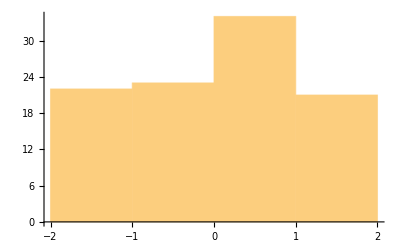

```mathematica
Histogram[%]
```

## Assignment 10: Temperature Converter

Create a temperature converter function. There should be two inputs and one output. The first input should be the temperature you wish to convert. The second input should be a string, either “FtoC” or “CtoF”. Based on the value of the string, the program should convert from Fahrenheit to Celsius or vice versa and output a decimal number.

```mathematica
Clear[t]
```

```mathematica
tempconverter[t_,stringinput_]:=Module[{tnew=t},
If[stringinput=="FtoC",tnew=(5*(t-32))/9];
If[stringinput=="CtoF",tnew=((9*5)*t)+32];
tnew
]
```

```mathematica
tempconverter [0,"CtoF"]
```

32

```mathematica
tempconverter[32,"FtoC"]
```

0